```mathematica
Clear[data,dataFit,λ0,λl,Ic,I0]
```

```mathematica
data=Import["/Users/timur/Documents/5 course/Мат. моделирование/2 семинар/Data.xlsx",{"Data",1}];
data=Delete[data,1];
```

```mathematica
data[[All,2]]=10^(data[[All,2]]/10);
```

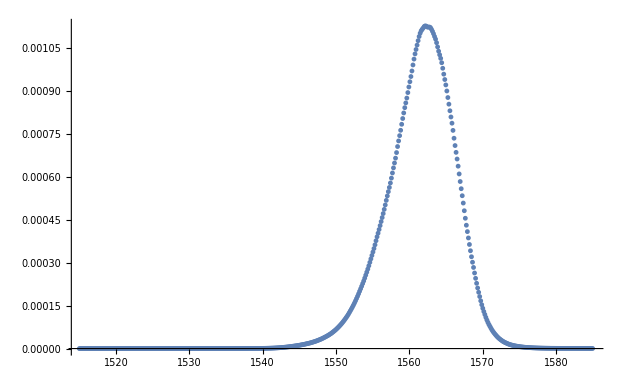

```mathematica
ListPlot[data,PlotRange->All]
```

```mathematica
gaussmodel=Ic+I0*Exp[-((λ-λ0)/λl)^2];
```

```mathematica
fit=FindFit[data,gaussmodel,{{Ic,0},{I0,0.001},{λ0,1563},{λl,5}},λ]
```

{Ic→4.79645×10^-6,I0→0.00110075,λ0→1562.09,λl→6.02531}

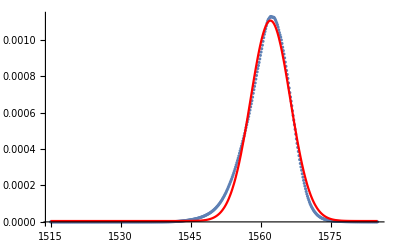

```mathematica
Show[ ListPlot[data, PlotRange->All],Plot[Evaluate[gaussmodel /. fit],{λ,Min[data[[All,1]]],Max[data[[All,1]]]}, PlotStyle->Red]]
```

```mathematica
dataFit=data[[180;;465]];
```

```mathematica
fit2=FindFit[dataFit,gaussmodel,{{Ic,0},{I0,0.001},{λ0,1563},{λl,5}},λ]
```

{Ic→0.000012971,I0→0.00109529,λ0→1562.09,λl→5.95873}

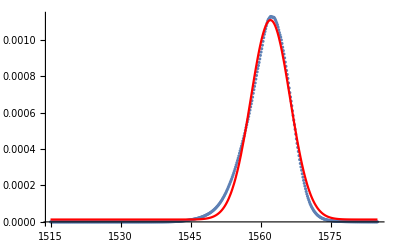

```mathematica
Show[ ListPlot[data, PlotRange->All],Plot[Evaluate[gaussmodel /. fit2],{λ,Min[data[[All,1]]],Max[data[[All,1]]]}, PlotStyle->Red]]
```